## 杨氏双缝干涉

光程差公式

```mathematica
r1=Sqrt[(x-d/2)^2+y^2+DD^2]
r2=Sqrt[(x+d/2)^2+y^2+DD^2]
𝔇[λ_]:=2 π (r2-r1)/λ
```

√(DD^2+(-d/2+x)^2+y^2)

√(DD^2+(d/2+x)^2+y^2)

光程差近似：

```mathematica
Simplify[Normal[Series[r2-r1, {x,0,2},{y,0,2},{d,0,2}]],Assumptions->DD>0]
```

(d x (2 DD^2-y^2))/(2 DD^3)

距离D=0.2m，狭缝距离1mm，波长分别为400nm，500nm，600nm 和 700nm的光入射的干涉条纹，中心都是亮纹：

```mathematica
condition={d-> 1 10^-3,DD-> 2 10^-1};
Grid[{Table[DensityPlot[4 Cos[𝔇[λ1 10^-9]]^2 /. condition, {x, -4 10^-4, 4 10^-4}, {y, -1 10^-4, 1 10^-4}, AspectRatio -> 1/8, PlotPoints -> 80, ImageSize -> 500, ColorFunction -> (Darker[ColorData["VisibleSpectrum"][λ1], 1 - #] &)], {λ1, 400, 700, 100}]}ᵀ]
```

-Graphics-

如果观察位置是x=-0.2m的平面，平行于yz平面，波长633nm，观察环形干涉：

```mathematica
Module[{},
 condition = {d -> 1 10^-3, x -> -2 10^-1};
 DensityPlot[1 + Cos[𝔇[633 10^-9]] /. condition, {y, -2 10^-2, 2 10^-2}, {DD, -2 10^-2, 2 10^-2}, PlotPoints -> 50, ColorFunction -> (Darker[ColorData["VisibleSpectrum"][633], #] &)]
 ]
```

-Graphics-

## 白光干涉

白光使用黑体辐射光源，参数是黑体温度T

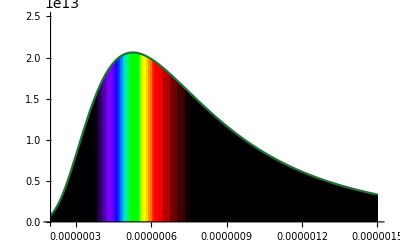

```mathematica
BBRSpectrum[λ_, T_] := With[{h = 6.6262 10^-34, c = 2.99792458 10^8, k = 1.3807 10^-23}, (2 h c^2/λ^5 )/(Exp[h c/(λ k T)] - 1)]
Plot[BBRSpectrum[λ,5500],{λ,200 10^-9,1500 10^-9},ColorFunction->(ColorData["VisibleSpectrum"][10^9#]&),Filling->Axis,ColorFunctionScaling->False,PlotRange->{0,2.5 10^13}]
```

在观察屏的不同位置上光谱是不一样的：

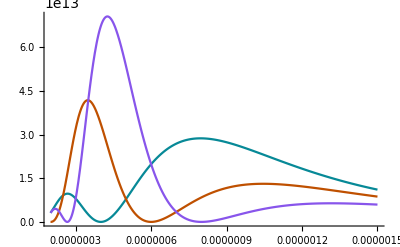

```mathematica
condition={d-> 1 10^-3,DD-> 2 10^-1};
Plot[{4 Cos[𝔇[λ]]^2*BBRSpectrum[λ , 5500] /. condition /. x -> 2 10^-5 /. y -> 0,
  4 Cos[𝔇[λ]]^2*BBRSpectrum[λ , 5500] /. condition /. x -> 3 10^-5 /. y -> 0,
  4 Cos[𝔇[λ]]^2*BBRSpectrum[λ, 5500] /. condition /. x -> 4 10^-5 /. y -> 0}, {λ, 200 10^-9, 1500 10^-9}, PlotRange -> All, PlotPoints -> 200]
```

为了把光谱强度变成颜色需要人眼视觉曲线：

Vos, J. J. (1978). Colorimetric and photometric properties of a 2-deg fundamental observer. Color Research and Application, 3, 125-128.

```mathematica
{λc, xc, yc, zc} = Import[FileNameJoin[{NotebookDirectory[],"ciexyzjv.csv"}]]ᵀ;
```

使用绘图

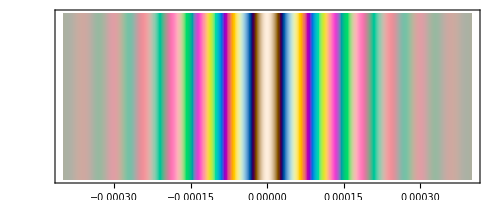

```mathematica
condition={d-> 1 10^-3,DD-> 2 10^-1};
XYZ[x1_]:={xc,yc,zc}.(4Cos[𝔇[λc  10^-9]]^2*BBRSpectrum[λc 10^-9,5500]/.condition/.x-> x1/.y-> 0)
Graphics[Table[{XYZColor @@ (XYZ[i 10^-6]/(2 10^15)), Rectangle[{i 10^-6, 0}, {(i + 1) 10^-6, 10^-4}]}, {i, -400, 400, 1}], Frame -> True, FrameTicks -> {Automatic, None, None, None}]
```